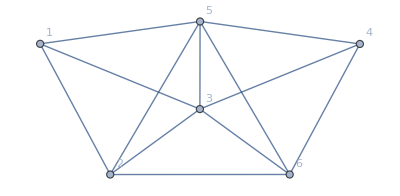

```mathematica
Graph[ReadGraph[6,1],VertexLabels->"Name"]
```

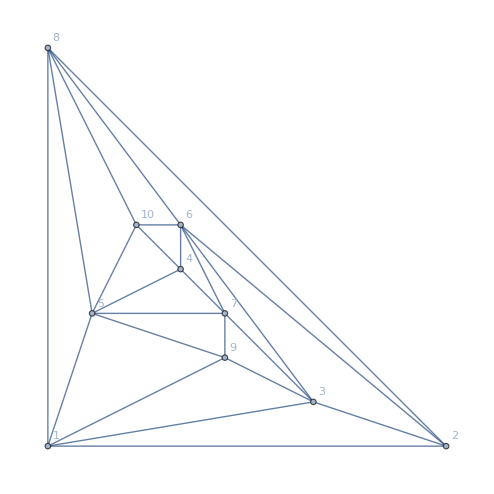
{-Graphics-,{{6,20},{5,20},{3,15},{1,15},{9,10},{8,10},{7,10},{2,10},{10,5},{4,5}},{{3<->6,17},{1<->5,17},{5<->9,14},{3<->9,14},{2<->6,14},{1<->2,14},{7<->9,11},{1<->9,11},{2<->8,11},{2<->3,11},{5<->8,10},{6<->7,10},{1<->3,10},{6<->8,9},{5<->7,9},{6<->10,8},{5<->10,8},{1<->8,8},{3<->7,8},{4<->6,8},{4<->5,8},{8<->10,7},{4<->10,7},{4<->7,7}}}

```mathematica
With[
{gr=ReadGraph[10,112]},
{Graph[gr,VertexLabels->"Name", GraphLayout->"PlanarEmbedding"],
Sort[Table[{v,ChromaticPolynomial[VertexDelete[gr,v],4]/24},{v,VertexList[gr]}],#1[[2]]>#2[[2]]&],
Sort[Table[{e,ChromaticPolynomial[EdgeDelete[gr,e],4]/24},{e,EdgeList[gr]}],#1[[2]]>#2[[2]]&]}
]
```

```mathematica
ColorData["Indexed"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113}

```mathematica
ColorData[113,"ColorList"]
```

{RGBColor[0.9, 0.27, 0.],RGBColor[0.97331, 0.616548, 0.0720638],RGBColor[0.672892, 0.38748, 0.61777],RGBColor[0.873133, 0.420301, 0.0828321],RGBColor[0.402478, 0.548513, 0.8],RGBColor[0.783249, 0.374, 0.42577],RGBColor[0.919858, 0.523239, 0.0718724],RGBColor[0.608835, 0.424846, 0.777912],RGBColor[0.8899440988397272, 0.3717565232487636, 0.19962732559818178],RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213],RGBColor[0.7274260891371029, 0.374, 0.5116521705583033],RGBColor[0.8810465843002272, 0.46723292150113577, 0.059192856109477554],RGBColor[0.5203677054097946, 0.47778136435093294, 0.799701860478545],RGBColor[0.8423167732415454, 0.36553664535169095, 0.3294720445974244],RGBColor[0.958279505801363, 0.5793074563814994, 0.08115093313273605]}

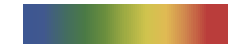

```mathematica
ColorData["DarkRainbow","Panel"]
```

```mathematica
RGBColor[0.79045296, 0.7551332, 0.29875856]RGBColor[0.7929021199999999, 0.45166319999999993, 0.28605948]RGBColor[0.60818824, 0.6638654399999999, 0.26249792]RGBColor[0.26875204, 0.43168736, 0.36674176]
```

```mathematica
With[
{gr=ReadGraph[5,1]},
Table[Style[e,ColorData[43,"ColorList"][[ ChromaticPolynomial[EdgeDelete[gr,e],4]/24 ]]],{e,EdgeList[gr]}]
]
```

{1<->2,1<->3,2<->3,2<->4,3<->4,1<->5,4<->5,2<->5,3<->5}

Table::iterb: Iterator {e, EdgeList[gr]} does not have appropriate bounds.

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[EdgeDelete[gr, e], 4].

Part::pkspec1: The expression 1/24\ ChromaticPolynomial[EdgeDelete[gr, e], 4] cannot be used as a part specification.

Table[Style[e,ColorData[Rainbow]⟦1/24 ChromaticPolynomial[EdgeDelete[gr,e],4]⟧],{e,EdgeList[gr]}]

```mathematica
With[
{gr=ReadGraph[10,112]},
Join[
Table[Style[e,ColorData[1,"ColorList"][[ ChromaticPolynomial[EdgeDelete[gr,e],4]/24 ]]],{e,EdgeList[gr]}],
Table[{v,ColorData[113,"ColorList"][[ ChromaticPolynomial[VertexDelete[gr,v],4]/24 ]]},{v,VertexList[gr]}]
]
]
```

Part::partw: Part 17 of … does not exist.

Part::partw: Part 20 of … does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{1<->2,1<->3,2<->3,Style[1<->5,{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.42664098839727194, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24],RGBColor[0.24, 0.47354534880363613, 0.6],RGBColor[0.5163614825959097, 0.24, 0.6],RGBColor[0.6, 0.3062683139954558, 0.24],RGBColor[0.3838248546049982, 0.6, 0.24],RGBColor[0.24, 0.5939180232054561, 0.6],RGBColor[0.39598880819409377, 0.24, 0.6],RGBColor[0.6, 0.24, 0.2941043604063603]}⟦17⟧],4<->5,2<->6,4<->6,Style[3<->6,{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.42664098839727194, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24],RGBColor[0.24, 0.47354534880363613, 0.6],RGBColor[0.5163614825959097, 0.24, 0.6],RGBColor[0.6, 0.3062683139954558, 0.24],RGBColor[0.3838248546049982, 0.6, 0.24],RGBColor[0.24, 0.5939180232054561, 0.6],RGBColor[0.39598880819409377, 0.24, 0.6],RGBColor[0.6, 0.24, 0.2941043604063603]}⟦17⟧],3<->7,4<->7,5<->7,6<->7,2<->8,5<->8,1<->8,6<->8,3<->9,5<->9,1<->9,7<->9,5<->10,6<->10,4<->10,8<->10,{1,RGBColor[0.958279505801363, 0.5793074563814994, 0.08115093313273605]},{2,RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213]},{3,RGBColor[0.958279505801363, 0.5793074563814994, 0.08115093313273605]},{5,{RGBColor[0.9, 0.27, 0.],RGBColor[0.97331, 0.616548, 0.0720638],RGBColor[0.672892, 0.38748, 0.61777],RGBColor[0.873133, 0.420301, 0.0828321],RGBColor[0.402478, 0.548513, 0.8],RGBColor[0.783249, 0.374, 0.42577],RGBColor[0.919858, 0.523239, 0.0718724],RGBColor[0.608835, 0.424846, 0.777912],RGBColor[0.8899440988397272, 0.3717565232487636, 0.19962732559818178],RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213],RGBColor[0.7274260891371029, 0.374, 0.5116521705583033],RGBColor[0.8810465843002272, 0.46723292150113577, 0.059192856109477554],RGBColor[0.5203677054097946, 0.47778136435093294, 0.799701860478545],RGBColor[0.8423167732415454, 0.36553664535169095, 0.3294720445974244],RGBColor[0.958279505801363, 0.5793074563814994, 0.08115093313273605]}⟦20⟧},{4,RGBColor[0.402478, 0.548513, 0.8]},{6,{RGBColor[0.9, 0.27, 0.],RGBColor[0.97331, 0.616548, 0.0720638],RGBColor[0.672892, 0.38748, 0.61777],RGBColor[0.873133, 0.420301, 0.0828321],RGBColor[0.402478, 0.548513, 0.8],RGBColor[0.783249, 0.374, 0.42577],RGBColor[0.919858, 0.523239, 0.0718724],RGBColor[0.608835, 0.424846, 0.777912],RGBColor[0.8899440988397272, 0.3717565232487636, 0.19962732559818178],RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213],RGBColor[0.7274260891371029, 0.374, 0.5116521705583033],RGBColor[0.8810465843002272, 0.46723292150113577, 0.059192856109477554],RGBColor[0.5203677054097946, 0.47778136435093294, 0.799701860478545],RGBColor[0.8423167732415454, 0.36553664535169095, 0.3294720445974244],RGBColor[0.958279505801363, 0.5793074563814994, 0.08115093313273605]}⟦20⟧},{7,RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213]},{8,RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213]},{9,RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213]},{10,RGBColor[0.402478, 0.548513, 0.8]}}

```mathematica
Beautify[gr_]:={HighlightGraph[ Graph[gr,VertexLabels->"Name",VertexSize->Large, GraphLayout->"PlanarEmbedding"],Join[
Table[Style[e,Thick,ColorData[113,"ColorList"][[ ChromaticPolynomial[EdgeDelete[gr,e],4]/24 ]]],{e,EdgeList[gr]}],
Table[Style[v,ColorData[113,"ColorList"][[ ChromaticPolynomial[VertexDelete[gr,v],4]/24 ]]],{v,VertexList[gr]}]
]],
Sort[Table[{v,ChromaticPolynomial[VertexDelete[gr,v],4]/24},{v,VertexList[gr]}],#1[[2]]>#2[[2]]&],
Sort[Table[{e,ChromaticPolynomial[EdgeDelete[gr,e],4]/24},{e,EdgeList[gr]}],#1[[2]]>#2[[2]]&]}
```

```mathematica
Beautify2[gr_]:=HighlightGraph[ Graph[gr,VertexSize->Large, GraphLayout->"PlanarEmbedding",
VertexLabels->Table[v->Style[ {v,ChromaticPolynomial[VertexDelete[gr,v],4]/24},Darker[Green]] ,{v,VertexList[gr]}],
EdgeLabels->Table[e[[1]]<->e[[2]]->Style[ ChromaticPolynomial[EdgeDelete[gr,e],4]/24,Bold,Red] ,{e,EdgeList[gr]}]
],Join[
Table[Style[e,Thick,ColorData[113,"ColorList"][[ ChromaticPolynomial[EdgeDelete[gr,e],4]/24 ]]],{e,EdgeList[gr]}],
Table[Style[v,ColorData[113,"ColorList"][[ ChromaticPolynomial[VertexDelete[gr,v],4]/24 ]]],{v,VertexList[gr]}]
]]
```

```mathematica
Beautify3[gr_]:=Graph[gr,VertexSize->Medium, GraphLayout->"PlanarEmbedding",
VertexLabels->Table[v->Style[ {v,ChromaticPolynomial[VertexDelete[gr,v],4]/24},Darker[Green]] ,{v,VertexList[gr]}],
EdgeLabels->Table[e[[1]]<->e[[2]]->Style[ ChromaticPolynomial[EdgeDelete[gr,e],4]/24,Bold,Red] ,{e,EdgeList[gr]}]
]
```

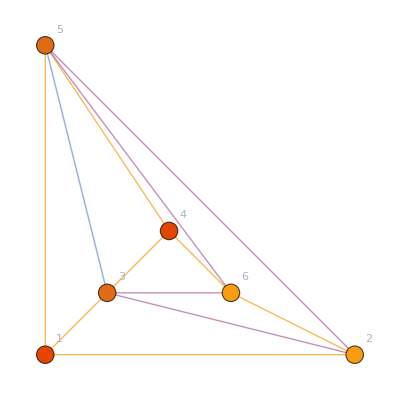
{-Graphics-,{{5,4},{3,4},{6,2},{2,2},{4,1},{1,1}},{{3<->5,5},{5<->6,3},{3<->6,3},{2<->5,3},{2<->3,3},{4<->6,2},{2<->6,2},{4<->5,2},{1<->5,2},{3<->4,2},{1<->3,2},{1<->2,2}}}

```mathematica
With[
{gr=ReadGraph[6,1]},
{HighlightGraph[ Graph[gr,VertexLabels->"Name",VertexSize->Medium, GraphLayout->"PlanarEmbedding"],Join[
Table[Style[e,Thick,ColorData[113,"ColorList"][[ ChromaticPolynomial[EdgeDelete[gr,e],4]/24 ]]],{e,EdgeList[gr]}],
Table[Style[v,ColorData[113,"ColorList"][[ ChromaticPolynomial[VertexDelete[gr,v],4]/24 ]]],{v,VertexList[gr]}]
]],
Sort[Table[{v,ChromaticPolynomial[VertexDelete[gr,v],4]/24},{v,VertexList[gr]}],#1[[2]]>#2[[2]]&],
Sort[Table[{e,ChromaticPolynomial[EdgeDelete[gr,e],4]/24},{e,EdgeList[gr]}],#1[[2]]>#2[[2]]&]}
]
```

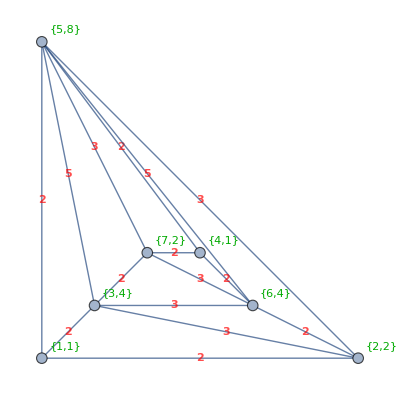

```mathematica
Beautify3[ReadGraph[7,1]]
```

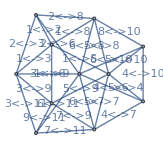

```mathematica
Graph[ReadGraph[11,914],EdgeLabels->Table[{e[[1]<->e[[2]]->]
```

```mathematica
Graph[dd,EdgeLabels->"Name"
```

Part::partw: Part 16 of … does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

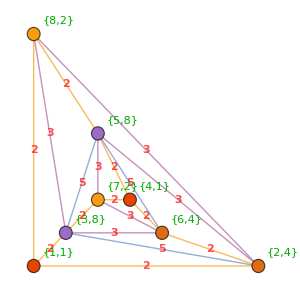
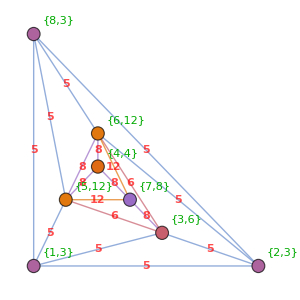
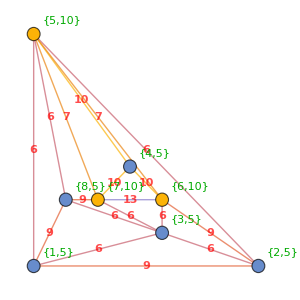
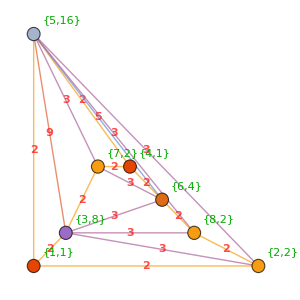
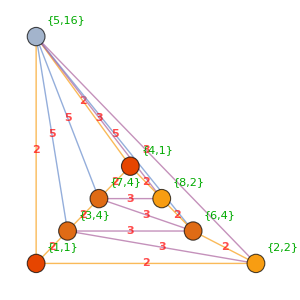
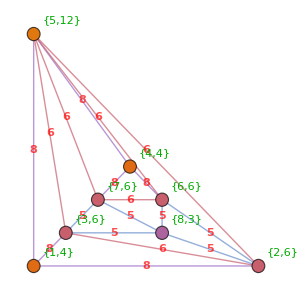
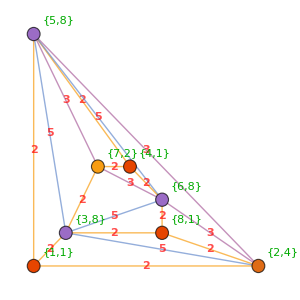
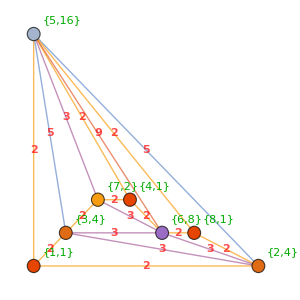

```mathematica
Table[Show[Beautify2[ReadGraph[8,k]],ImageSize->300],{k,1,14}]
```

```mathematica
EdgeContract
```

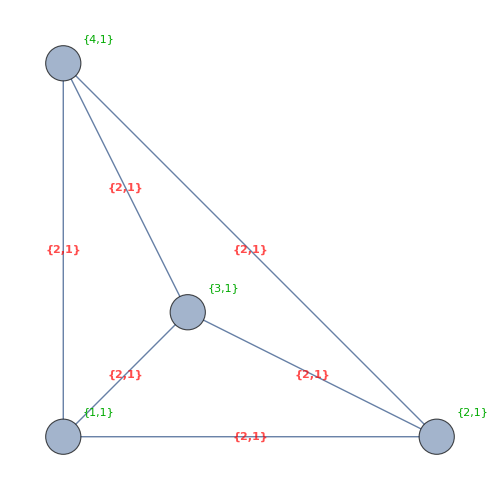
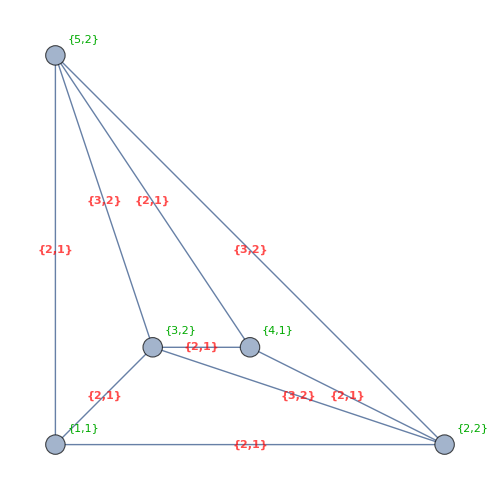
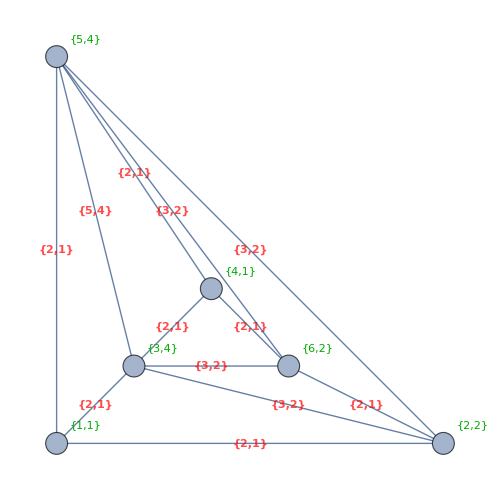
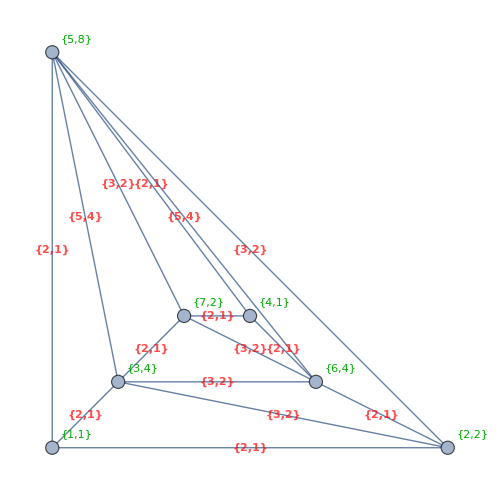

```mathematica
Table[
Show[Beautify4[ReadGraph[k[[1]],k[[2]]]],ImageSize->500],
{k,{{4,1},{5,1},{6,1},{7,1}}}]
```

```mathematica
&é
```

```mathematica
Beautify4[gr_]:=Graph[gr,VertexSize->Medium, GraphLayout->"PlanarEmbedding",
VertexLabels->Table[v->Style[ {v,ChromaticPolynomial[VertexDelete[gr,v],4]/24},Darker[Green]] ,{v,VertexList[gr]}],
EdgeLabels->Table[e[[1]]<->e[[2]]->Style[ {ChromaticPolynomial[EdgeDelete[gr,e],4]/24,ChromaticPolynomial[EdgeContract[gr,e],4]/24},Bold,Red] ,{e,EdgeList[gr]}]
]
```